```mathematica
f[x_]:=(1-x)/(1+x)- ϵ x^3
```

```mathematica
x1=1-(2 ϵ)/5
```

1-(2 ϵ)/5

```mathematica
x2=1/ϵ^(1/3)(-1-ϵ^(1/3) (2/5))
```

(-1-(2 ϵ^(1/3))/5)/ϵ^(1/3)

```mathematica
f1[ϵ_]:=f[ϵ]/.x->x1
```

```mathematica
f2[ϵ_]:=f[ϵ]/.x->x2
```

```mathematica
graphf1=Plot[f1[ϵ],{ϵ,0,4},AxesLabel->{"t","y"},PlotLabel->"Analytic Solution of y"];
graphf2=Plot[f2[ϵ],{ϵ,0,4},AxesLabel->{"t","y"},PlotLabel->"Analytic Solution of y"];
```

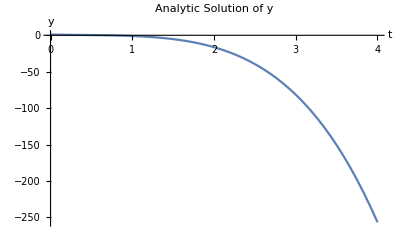

```mathematica
Show[graphf1]
```

```mathematica
Show[graphf2]
```

-Graphics-